```mathematica
"Modern Cosmology Chapter 1";
"Exe.1";

Subscript[T, 0]=2.725;
T=10^(19+9);
Subscript[ρ, Λ]=0.7*(Subscript[T, 0]/T)^4
```

3.85979×10^-111

```mathematica
"Exe.2";
Subscript[Ω, Λ]=0.7;
Integrate[D[H0^-1*1/a(Subscript[Ω, Λ]+(1-Subscript[Ω, Λ])/a^3),a],a]
```

0.3/(a^4 H0)+0.7/(a H0)

2.725

(7.6526×10^-20)/((-1+ⅇ^(0.000841302/λ)) λ^5)

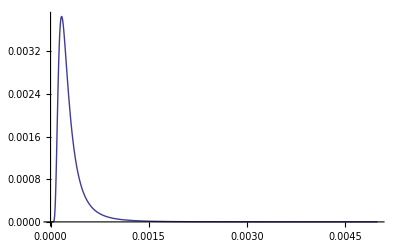

```mathematica
"Exe.4";
c=3*^8;
v[λ_]=c/(2*π*λ);
h=1.054571628*^-34;
kb=1.38*^-23;
T=2.725
Iλ[λ_]=-(4*π*h*v[λ]^3/c^2)/(Exp[2*π*h*v[λ]/kb/T]-1)*D[v[λ],λ]
Plot[Iλ[x],{x,0,0.005},PlotRange->Full]
```